```mathematica
ClearAll
```

ClearAll

```mathematica
n0=-5;
nf=15;
logk0=-4;
logkf=1;
k0=10^logk0;
kf=10^logkf;
t0=-Exp[-n0];
tf=-Exp[-nf];
step=0.2;
bstep=1;
```

```mathematica
ζ[t_]=(1+ⅈ*k*t)*Exp[-ⅈ*k*t];
cζ[t_]:=(1-ⅈ*k*t)*Exp[ⅈ*k*t];
(*η[t_]:=Exp[-(-Log[-t]+2)^2]*)
η[t_]:=0.05
```

```mathematica
list=List[];
list2=List[];
list3=List[];
list4=List[];
Plist=List[];
```

```mathematica
Do[{s=NDSolve[{x1'[t]==-ⅈ*η[t]/(k^3*t^3)*(D[cζ[t],t]*ζ[t]*y1[t]+D[cζ[t],t]*cζ[t]*y2[t]), x2'[t]==-ⅈ*η[t]/(k^3*t^3)*(-D[ζ[t],t]*ζ[t]*y1[t]+-D[ζ[t],t]*cζ[t]*y2[t]),y1'[t]==ⅈ*η[t]/(k^3*t^3)*(-D[ζ[t],t]*cζ[t]*x1[t]+-D[cζ[t],t]*cζ[t]*x2[t]),
y2'[t]==ⅈ*η[t]/(k^3*t^3)*(D[ζ[t],t]*ζ[t]*x1[t]+D[cζ[t],t]*ζ[t]*x2[t]), x1[t0]==1, x2[t0]==0, y1[t0]==0, y2[t0]==0},{x1,x2,y1,y2},{t,t0,tf}], xx2[t_]:=x2[t]/.s, points1=Table[{k,n,xx2[-Exp[-n]]},{n,n0,nf,step}], nk=points1[[(nf-n0+bstep*step)/step]],AppendTo[list,{nk[[1]],nk[[3]][[1]]}], xx1[t_]:=x1[t]/.s, points2=Table[{k,n,xx1[-Exp[-n]]},{n,n0,nf,step}], nk2=points2[[(nf-n0+bstep*step)/step]],AppendTo[list2,{nk2[[1]],nk2[[3]][[1]]}] }, {k,10^Range[logk0,logkf,step]}]
```

```mathematica
Do[{s2=NDSolve[{x1'[t]==-ⅈ*η[t]/(k^3*t^3)*(D[cζ[t],t]*ζ[t]*y1[t]+D[cζ[t],t]*cζ[t]*y2[t]), x2'[t]==-ⅈ*η[t]/(k^3*t^3)*(-D[ζ[t],t]*ζ[t]*y1[t]+-D[ζ[t],t]*cζ[t]*y2[t]),y1'[t]==ⅈ*η[t]/(k^3*t^3)*(-D[ζ[t],t]*cζ[t]*x1[t]+-D[cζ[t],t]*cζ[t]*x2[t]),
y2'[t]==ⅈ*η[t]/(k^3*t^3)*(D[ζ[t],t]*ζ[t]*x1[t]+D[cζ[t],t]*ζ[t]*x2[t]), x1[t0]==0, x2[t0]==0, y1[t0]==1, y2[t0]==0},{x1,x2,y1,y2},{t,t0,tf}], xx22[t_]:=x2[t]/.s2, points3=Table[{k,n,xx22[-Exp[-n]]},{n,n0,nf,step}], nk3=points3[[(nf-n0+bstep*step)/step]],AppendTo[list3,{nk3[[1]],nk3[[3]][[1]]}], xx11[t_]:=x1[t]/.s2, points4=Table[{k,n,xx11[-Exp[-n]]},{n,n0,nf,step}], nk4=points4[[(nf-n0+bstep*step)/step]],AppendTo[list4,{nk4[[1]],nk4[[3]][[1]]}] }, {k,10^Range[logk0,logkf,step]}]
```

```mathematica
list;
```

```mathematica
Print[nk2[[2]]]
```

15.

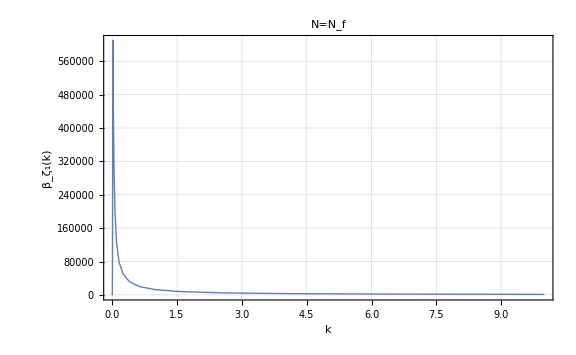

```mathematica
ListLinePlot[Re[list], PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["k", Black, FontSize->24],Style["β_ζ_1(k)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, GridLines->Automatic, GridLinesStyle->{{Black, Dotted, Thickness[0.001]}, {Black, Dotted, Thickness[0.001]}}, PlotLabel->Style["N=N_f", Black, FontSize->20], PlotRange->All]
```

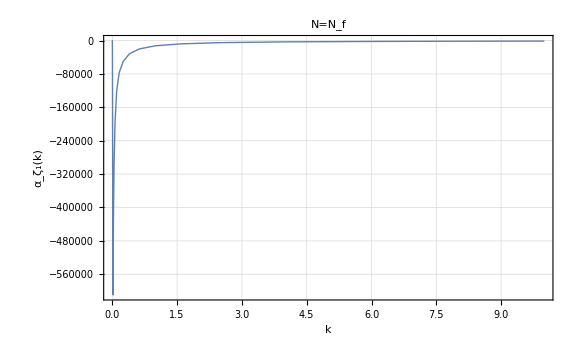

```mathematica
ListLinePlot[Re[list2], PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["k", Black, FontSize->24],Style["α_ζ_1(k)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, GridLines->Automatic, GridLinesStyle->{{Black, Dotted, Thickness[0.001]}, {Black, Dotted, Thickness[0.001]}}, PlotLabel->Style["N=N_f", Black, FontSize->20], PlotRange->All]
```

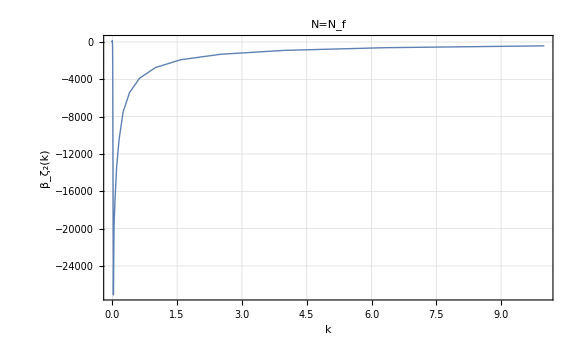

```mathematica
ListLinePlot[Re[list3], PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["k", Black, FontSize->24],Style["β_ζ_2(k)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, GridLines->Automatic, GridLinesStyle->{{Black, Dotted, Thickness[0.001]}, {Black, Dotted, Thickness[0.001]}}, PlotLabel->Style["N=N_f", Black, FontSize->20], PlotRange->All]
```

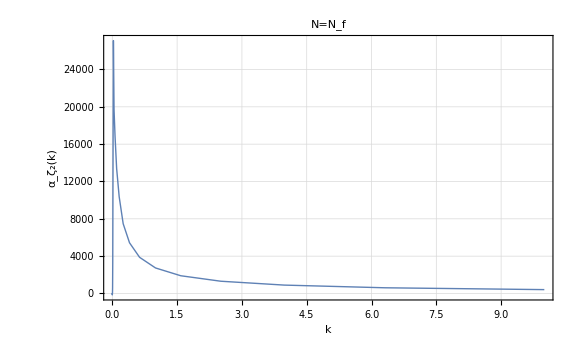

```mathematica
ListLinePlot[Re[list4], PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["k", Black, FontSize->24],Style["α_ζ_2(k)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, GridLines->Automatic, GridLinesStyle->{{Black, Dotted, Thickness[0.001]}, {Black, Dotted, Thickness[0.001]}}, PlotLabel->Style["N=N_f", Black, FontSize->20], PlotRange->All]
```

```mathematica
Do[AppendTo[Plist,List[list[[i]][[1]],(Abs[list[[i]][[2]]+list2[[i]][[2]]])^2+(Abs[list3[[i]][[2]]+ list4[[i]][[2]]])^2]],{i,1,Length[10^Range[logk0,logkf,step]]}]
Plist;
```

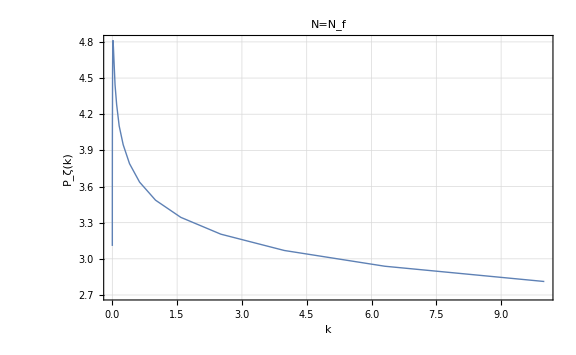

```mathematica
ListLinePlot[Plist, PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["k", Black, FontSize->24],Style["P_ζ(k)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, GridLines->Automatic, GridLinesStyle->{{Black, Dotted, Thickness[0.001]}, {Black, Dotted, Thickness[0.001]}}, PlotLabel->Style["N=N_f", Black, FontSize->20], PlotRange->All]
```

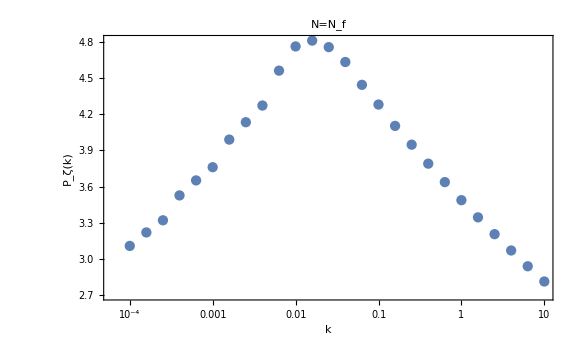

```mathematica
ListLogLinearPlot[Plist, PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["k", Black, FontSize->24],Style["P_ζ(k)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, GridLines->Automatic, GridLinesStyle->{{Black, Dotted, Thickness[0.001]}, {Black, Dotted, Thickness[0.001]}}, PlotLabel->Style["N=N_f", Black, FontSize->20], PlotRange->All, Joined->False]
```